Computing the eigenvalues of H using numerical approach

### The q-ratio is properly chosen and avoids strong oscillating behavior of λ near certain points across q-interval

```mathematica
matEl[n_,m_,e_,v_]:=Piecewise[{{n*e,n-m==0},{Sqrt[m+1]Sqrt[m+2](-v),n-m==2},{Sqrt[m]Sqrt[m-1](-v),n-m==-2 }}];
Hmat02[n_,e_,v_]:=Table[Table[matEl[2(i-1),2(j-1),e,v],{j,1,n}],{i,1,n}];
Hmat13[n_,e_,v_]:=Table[Table[matEl[2i+1,2j+1,e,v],{j,0,n-1}],{i,0,n-1}];
```

```mathematica
boson0[n_,q_]:=Hmat02[n,1,q];
boson1[n_,q_]:=Hmat13[n,1,q];
```

Solutions of the matrix Hamiltonian

```mathematica
sol0[n_,q_]:=Eigenvalues[boson0[n,q]];
sol1[n_,q_]:=Eigenvalues[boson1[n,q]];
```

Evolution of λ with the ratio q

```mathematica
lambdaQ[n_,id_,p_]:=sol0[n,q][[id]]/.{q->p};
```

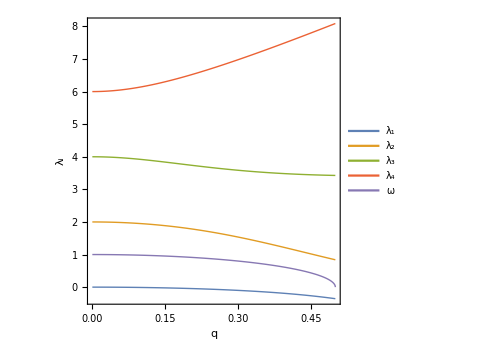

```mathematica
Plot[{lambdaQ[4,1,p],lambdaQ[4,2,p],lambdaQ[4,3,p],lambdaQ[4,4,p],Sqrt[1-4p^2]},{p,0,0.5},AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],LabelStyle->{Black,20,Bold,FontFamily->"Times New Roman"},FrameLabel->{"q",Subscript["λ","i"]},PlotLegends->Placed[{"λ_1","λ_2","λ_3","λ_4","ω"},{0.15,0.7}],ImageSize->Medium,PlotStyle->Thick]
```